## Set up activation functions and derivatives

```mathematica
f[x_] := 1./(1+Exp[-x])
fp[x_] = D[f[x],{x,1}]
fpp[x_] = D[f[x],{x,2}]
```

(1. ⅇ^-x)/((1+ⅇ^-x)^2)

1. ((2 ⅇ^(-2 x))/((1+ⅇ^-x)^3)-ⅇ^-x/((1+ⅇ^-x)^2))

## Now set up exact function and derivatives (3 neurons, all weights=1)

```mathematica
F[x_] := f[ f[  f[x]]]
Fp[x_] = D[F[x],x]
Fpp[x_] = D[F[x],{x,2}]
```

(1. ⅇ^(-1./(1+ⅇ^(-1./(1+ⅇ^-x)))-1./(1+ⅇ^-x)-x))/((1+ⅇ^(-1./(1+ⅇ^(-1./(1+ⅇ^-x)))))^2 (1+ⅇ^(-1./(1+ⅇ^-x)))^2 (1+ⅇ^-x)^2)

1. ((2. ⅇ^(-2./(1+ⅇ^(-1./(1+ⅇ^-x)))-2./(1+ⅇ^-x)-2 x))/((1+ⅇ^(-1./(1+ⅇ^(-1./(1+ⅇ^-x)))))^3 (1+ⅇ^(-1./(1+ⅇ^-x)))^4 (1+ⅇ^-x)^4)+(2. ⅇ^(-1./(1+ⅇ^(-1./(1+ⅇ^-x)))-2./(1+ⅇ^-x)-2 x))/((1+ⅇ^(-1./(1+ⅇ^(-1./(1+ⅇ^-x)))))^2 (1+ⅇ^(-1./(1+ⅇ^-x)))^3 (1+ⅇ^-x)^4)+(2. ⅇ^(-1./(1+ⅇ^(-1./(1+ⅇ^-x)))-1./(1+ⅇ^-x)-2 x))/((1+ⅇ^(-1./(1+ⅇ^(-1./(1+ⅇ^-x)))))^2 (1+ⅇ^(-1./(1+ⅇ^-x)))^2 (1+ⅇ^-x)^3)+(1. ⅇ^(-1./(1+ⅇ^(-1./(1+ⅇ^-x)))-1./(1+ⅇ^-x)-x) (-1-(1. ⅇ^-x)/((1+ⅇ^-x)^2)-(1. ⅇ^(-1./(1+ⅇ^-x)-x))/((1+ⅇ^(-1./(1+ⅇ^-x)))^2 (1+ⅇ^-x)^2)))/((1+ⅇ^(-1./(1+ⅇ^(-1./(1+ⅇ^-x)))))^2 (1+ⅇ^(-1./(1+ⅇ^-x)))^2 (1+ⅇ^-x)^2))

## Define network-type function

```mathematica
g[x_] := Module[{zi=x},
wij=1;
wjk=1;
zj=wij *f[zi];
zk = wjk * f[zj];
dajdzi=wij fp[zj] fp[zi];
dakdzi = fp[zk] wij dajdzi;
d2ajdzi2=fpp[zj] (wij fp[zi])^2+fp[zj] wij fpp[zi];
d2akdzi2 = fpp[zk] (wjk dajdzi)^2 + fp[zk] wjk d2ajdzi2 ;
{f[zk],dakdzi,d2akdzi2}
]
```

## Compare exact vs. autodiff results

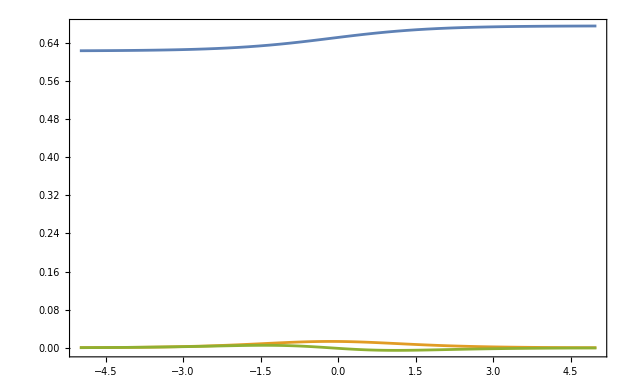

```mathematica
Plot[{F[x],Fp[x],Fpp[x]},{x,-5,5},PlotRange->All,Frame->True]
```

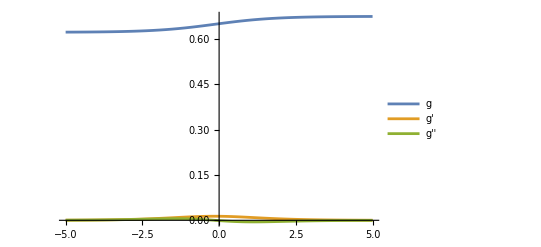

```mathematica
Plot[{g[x][[1]],g[x][[2]],g[x][[3]]},{x,-5,5},PlotLegends->{"g","g'","g''"}]
```

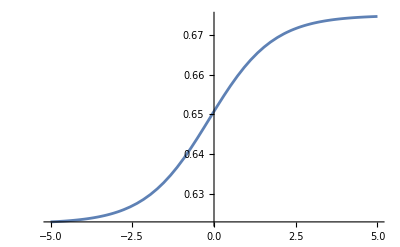

```mathematica
Plot[F[x],{x,-5,5}]
```